```mathematica
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]

SmashEigen[G0_,S0_]:=Module[{G=G0,S=S0},
Eigenvalues[Smash[G,S]]
]
```

```mathematica
(*Function to Split Eigenvalues into two groups per Corollary 2.2 [Kempton,Lippner,Yau]*)
SplitEigs[EigVals_, EigVecs_] := Module[{lambda=List[], mu = List[]},
For[j=1, j<=Length[EigVals], j++, 
If[EigVecs[[j]][[1]]== EigVecs[[j]][[-1]], AppendTo[lambda,EigVals[[j]]],
If [EigVecs[[j]][[1]]== -EigVecs[[j]][[-1]], AppendTo[mu,EigVals[[j]]],Print["No PST"];Break[]]]];
{lambda,mu}(*Print[lambda]; Print[mu]*)]
```

```mathematica
(*Helper Functions*)
IsRational[Val_]:= Element[Val,Rationals]
NotZero[Val_]:=IsRational[Val]&&Val!=0
IsReal[Val_]:=Not[Element[Val,Rationals]]

(*Determine if lambda1-lambda2 is rational per Corollary 2.2 [Kempton,Lippner,Yau]*)
CheckRationals[Lambdas_]:=Module[{combos=List[]},
For[i=1,i<=Length[Lambdas],i++,
For[j=1,j<=Length[Lambdas],j++,
AppendTo[combos,Simplify[Lambdas[[i]]-Lambdas[[j]]]]]];
If[AllTrue[combos,IsRational],Print["All Rationals"],
If[AnyTrue[combos, IsReal]&& AnyTrue[combos,NotZero],Print["No PST"],
(*Check every combination*)Print["GROSS"]]]]
```

```mathematica
NaiveCheckRationals[Lambdas_]:=Module[{combos=List[]},
For[i=1,i<=Length[Lambdas],i++,
For[j=1,j<=Length[Lambdas],j++,
AppendTo[combos,Simplify[Lambdas[[i]]-Lambdas[[j]]]]]];
For[i=1,i<=Length[combos],i++,
For[j=1,j<=Length[combos],j++,
If[combos[[j]]==0,Continue[],
If[Element[combos[[i]]/combos[[j]],Rationals],Continue[], Print["Bad Combo"];Print[combos[[i]]/combos[[j]]];Break[]]]]];
Print["All Rationals"]]
```

```mathematica
(*!!!CHECK!!! For every l-m/l1-l2, is the system of equations the same?*)
(*Determine if lambda1-mu2 is odd per Corollary 2.2 [Kempton,Lippner,Yau]*)
(*Compute every l-m, simplify, set equal to 2k+1, solve for L*)

(*Determine if lambda1-lambda2 is even per Corollary 2.2 [Kempton,Lippner,Yau]*)
(*Compute every l1-l2, simplify, set equal to 2n, solve for L*)
```

```mathematica
Solve[(1-Sqrt[1+2L^2])/L==(a+b Sqrt[D])/2, {a}]
```

{{a→(2-b √D L-2 √(1+2 L^2))/L}}

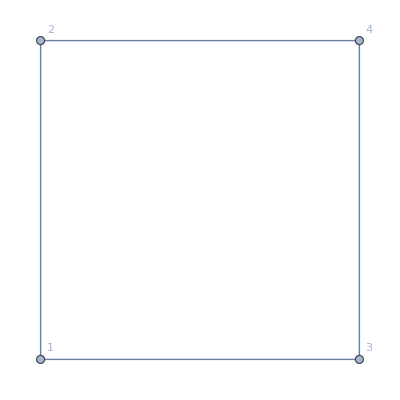

(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

{-2,2,0,0}

{{1,-1,-1,1},{1,1,1,1},{-1,0,0,1},{0,-1,1,0}}

```mathematica
(*2d Hypercube*)
G=HypercubeGraph[2,VertexLabels->"Name"]
MatrixForm[AdjacencyMatrix[G]]
Eigenvalues[AdjacencyMatrix[G]]
Eigenvectors[AdjacencyMatrix[G]]
```

```mathematica
(*Eigenvalue 2*)
Simplify[Smash[G,{1,3,4}]]
eval = Eigenvalues[Simplify[Smash[G, {1,3,4}]]]
evec = Eigenvectors[Simplify[Smash[G, {1,3,4}]]]
"Attempt to split Eigenvalues"
split=SplitEigs[eval,evec]
lambda=split[[1]]
mu=split[[2]]
"Attempt to Check The Rationals case"
combos=List[]
For[i=1,i<=Length[lambda],i++,
For[j=1,j<=Length[lambda],j++,
AppendTo[combos,Simplify[lambda[[i]]-lambda[[j]]]]]]
combos
AllTrue[combos,IsRational]
If[AllTrue[combos,IsRational],Print["All Rationals"],
If[AnyTrue[combos, IsReal]&& AnyTrue[combos,NotZero],Print["No PST"],
(*Check every combination*)Print["GROSS"]]]
(*CheckRationals[lambda]*)
NaiveCheckRationals[lambda]
mat = Simplify[Smash[G,{1,3,4}]] /. L -> Sqrt[15/2]
Simplify[MatrixExp[mat I t]]
Simplify[MatrixExp[mat I t] /. t -> Sqrt[15/2]π]
```

{{1/L,1,1/L},{1,0,1},{1/L,1,1/L}}

{0,(1-√(1+2 L^2))/L,(1+√(1+2 L^2))/L}

{{-1,0,1},{1,-(2 L)/(-1+√(1+2 L^2)),1},{1,(2 L)/(1+√(1+2 L^2)),1}}

Attempt to split Eigenvalues

{{(1-√(1+2 L^2))/L,(1+√(1+2 L^2))/L},{0}}

{(1-√(1+2 L^2))/L,(1+√(1+2 L^2))/L}

{0}

Attempt to Check The Rationals case

{}

{0,-(2 √(1+2 L^2))/L,(2 √(1+2 L^2))/L,0}

(√(1+2 L^2))/L∈ℚ&&(√(1+2 L^2))/L∈ℚ

If[(√(1+2 L^2))/L∈ℚ&&(√(1+2 L^2))/L∈ℚ,Print[All Rationals],If[AnyTrue[combos,IsReal]&&AnyTrue[combos,NotZero],Print[No PST],Print[GROSS]]]

All Rationals

{{√(2/15),1,√(2/15)},{1,0,1},{√(2/15),1,√(2/15)}}

{{1/16 (8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/16 (-8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t))},{1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/8 ⅇ^(-ⅈ √(6/5) t) (5+3 ⅇ^(8 ⅈ √(2/15) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t))},{1/16 (-8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t)),1/8 √(15/2) ⅇ^(-ⅈ √(6/5) t) (-1+ⅇ^(8 ⅈ √(2/15) t)),1/16 (8+3 ⅇ^(-ⅈ √(6/5) t)+5 ⅇ^(ⅈ √(10/3) t))}}

{{0,0,-1},{0,-1,0},{-1,0,0}}

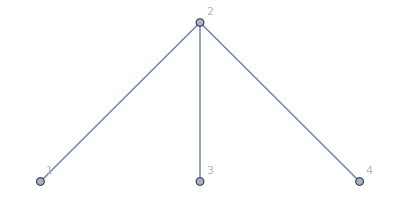

```mathematica
G=Graph[{1<->2,2<->3,2<->4},VertexLabels->"Name"]
```

```mathematica
MatrixForm[AdjacencyMatrix[G]]
GSmash=Simplify[Smash[G,{1,2,4}]]
Eigenvalues[GSmash]
Eigenvectors[GSmash]
```

(0 | 1 | 0 | 0
1 | 0 | 1 | 1
0 | 1 | 0 | 0
0 | 1 | 0 | 0)

{{0,1,0},{1,1/L,1},{0,1,0}}

{0,(1-√(1+8 L^2))/(2 L),(1+√(1+8 L^2))/(2 L)}

{{-1,0,1},{1,-(-1+√(1+8 L^2))/(2 L),1},{1,-(-1-√(1+8 L^2))/(2 L),1}}

```mathematica
Solve[(4L+1-L^2)/(-1+L^2)==2k+1,L]
```

{{L→(1-√(2+2 k+k^2))/(1+k)},{L→(1+√(2+2 k+k^2))/(1+k)}}

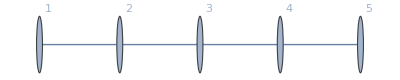

```mathematica
G=Graph[{1<->2,2<->3,3<->4,4<->5},VertexLabels->"Name"]
```

```mathematica
MatrixForm[AdjacencyMatrix[G]]
GSmash=Simplify[Smash[G,{1,3,5}]]
Eigenvalues[GSmash]
Eigenvectors[GSmash]
```

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{{1/L,1/L,0},{1/L,2/L,1/L},{0,1/L,1/L}}

{3/L,1/L,0}

{{1,2,1},{-1,0,1},{1,-1,1}}

```mathematica
"Equations to solve"
Simplify[MatrixExp[GSmash I t]]
"Knocks out L"
(*Using 6 intead of 2 fully simplifies to identity*)
Simplify[MatrixExp[GSmash I t]/.t->2L π/3]
"Without taking out L"
Simplify[MatrixExp[GSmash I t]/.t->2π/3]
```

Equations to solve

{{1/6 (2+3 ⅇ^((ⅈ t)/L)+ⅇ^((3 ⅈ t)/L)),1/3 (-1+ⅇ^((3 ⅈ t)/L)),1/6 (-1+ⅇ^((ⅈ t)/L))^2 (2+ⅇ^((ⅈ t)/L))},{1/3 (-1+ⅇ^((3 ⅈ t)/L)),1/3 (1+2 ⅇ^((3 ⅈ t)/L)),1/3 (-1+ⅇ^((3 ⅈ t)/L))},{1/6 (-1+ⅇ^((ⅈ t)/L))^2 (2+ⅇ^((ⅈ t)/L)),1/3 (-1+ⅇ^((3 ⅈ t)/L)),1/6 (2+3 ⅇ^((ⅈ t)/L)+ⅇ^((3 ⅈ t)/L))}}

Knocks out L

{{1/2 (1+(-1)^(2/3)),0,1/2 (1-(-1)^(2/3))},{0,1,0},{1/2 (1-(-1)^(2/3)),0,1/2 (1+(-1)^(2/3))}}

Without taking out L

{{1/6 (2+3 ⅇ^((2 ⅈ π)/(3 L))+ⅇ^((2 ⅈ π)/L)),1/3 (-1+ⅇ^((2 ⅈ π)/L)),1/6 (2-3 ⅇ^((2 ⅈ π)/(3 L))+ⅇ^((2 ⅈ π)/L))},{1/3 (-1+ⅇ^((2 ⅈ π)/L)),1/3 (1+2 ⅇ^((2 ⅈ π)/L)),1/3 (-1+ⅇ^((2 ⅈ π)/L))},{1/6 (2-3 ⅇ^((2 ⅈ π)/(3 L))+ⅇ^((2 ⅈ π)/L)),1/3 (-1+ⅇ^((2 ⅈ π)/L)),1/6 (2+3 ⅇ^((2 ⅈ π)/(3 L))+ⅇ^((2 ⅈ π)/L))}}

```mathematica
Solve[1/3 (-1+ⅇ^((3 ⅈ t)/L))==0,t]
Solve[1/6 (2+3 ⅇ^((ⅈ t)/L)+ⅇ^((3 ⅈ t)/L))==0,t]
(*This disparity shows no PST as t must be real and not complex*)
```

{{t→ConditionalExpression[(2 L π C[1])/3, C[1]∈ℤ]}}

{{t→ConditionalExpression[-ⅈ L (ⅈ π+2 ⅈ π C[1]+Log[-Root-0.596Root[2+3 #1+#1^3&,1]-0.5960716379833215]), C[1]∈ℤ]},{t→ConditionalExpression[-ⅈ L (2 ⅈ π C[1]+Log[Root0.298-1.81 ⅈRoot[2+3 #1+#1^3&,2]0.29803581899166076]), C[1]∈ℤ]},{t→ConditionalExpression[-ⅈ L (2 ⅈ π C[1]+Log[Root0.298+1.81 ⅈRoot[2+3 #1+#1^3&,3]0.29803581899166076]), C[1]∈ℤ]}}

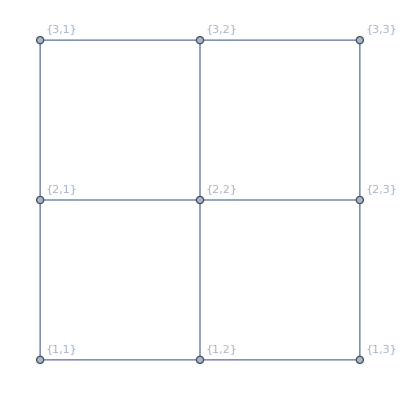

```mathematica
(*ClearAll["Global`*"]*)
G = GraphProduct[PathGraph[{1,2,3}],PathGraph[{1, 2, 3}], GraphLayout ->"GridEmbedding", VertexLabels->"Name"]
```

```mathematica
"Eigenvalues of Original Adjacency Matrix:"
Eigenvalues[AdjacencyMatrix[G]]
Gsmash = Simplify[Smash[G, {{1,1},{1,2},{1,3},{2,3},{3,3}}]]

"Eigenvalues of Reduced Matrix:"
Eigenvalues[Gsmash]
Simplify[Eigenvectors[Gsmash]]

mat = Gsmash /. L->-1

"Check PST for a given t:"
(*Simplify[MatrixExp[mat I t]]*)
```

Eigenvalues of Original Adjacency Matrix:

{-2 √2,2 √2,-√2,-√2,√2,√2,0,0,0}

{{(-2+L^2)/(L (-4+L^2)),(-3+L^2)/(-4+L^2),0,1/(-4+L^2),2/(L (-4+L^2))},{(-3+L^2)/(-4+L^2),(-2+L^2)/(L (-4+L^2)),1,(-2+L^2)/(L (-4+L^2)),1/(-4+L^2)},{0,1,0,1,0},{1/(-4+L^2),(-2+L^2)/(L (-4+L^2)),1,(-2+L^2)/(L (-4+L^2)),(-3+L^2)/(-4+L^2)},{2/(L (-4+L^2)),1/(-4+L^2),0,(-3+L^2)/(-4+L^2),(-2+L^2)/(L (-4+L^2))}}

Eigenvalues of Reduced Matrix:

{(-4+L^2-(-4+L^2) √(1+4 L^2))/(2 L (-4+L^2)),(-4+L^2+(-4+L^2) √(1+4 L^2))/(2 L (-4+L^2)),Root[32 L^4-16 L^6+2 L^8+(-40 L^2+22 L^4-3 L^6) #1+(4-3 L^2) #1^2+#1^3&,1]/(L (-4+L^2)),Root[32 L^4-16 L^6+2 L^8+(-40 L^2+22 L^4-3 L^6) #1+(4-3 L^2) #1^2+#1^3&,2]/(L (-4+L^2)),Root[32 L^4-16 L^6+2 L^8+(-40 L^2+22 L^4-3 L^6) #1+(4-3 L^2) #1^2+#1^3&,3]/(L (-4+L^2))}

{{-1/3,2/3,0,-1/3,2/3},{2/3,-1/3,1,-1/3,-1/3},{0,1,0,1,0},{-1/3,-1/3,1,-1/3,2/3},{2/3,-1/3,0,2/3,-1/3}}

Check PST for a given t: